# POE Lab 2 - 3D Scanner

## Voltage to Distance

```mathematica
distanceCSV=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Csv"];
distanceData=distanceCSV[[2;;Length[distanceCSV]-1]];
```

```mathematica
Fit[Map[Reverse,distanceData], {1,x,x^2,x^3},x]
```

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

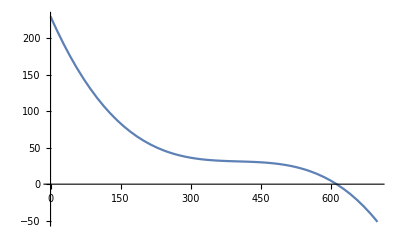

```mathematica
Plot[230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3,{x,0,700}]
```

## Make Functions voltageToDistance anglesToPan anglesToTilt panTiltDistance sphericalToCartesian-not sure if working correctly

```mathematica
voltageToDistance[x_]=(230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3);
anglesToPan[servo1_,servo2_]:=Module[{},(N@servo1-servo2)/2]
anglesToTilt[servo1_,servo2_]:=Module[{},(N@servo1+servo2)/2]
```

```mathematica
panTiltDistance[{servo1_,servo2_,voltage_}]:=Module[{pan,tilt,distance},
pan=anglesToPan[servo1,servo2];
tilt=anglesToTilt[servo1,servo2];
distance=voltageToDistance[voltage];
Return[{distance,tilt,pan}]
]
```

```mathematica
ClearAll@toCartesian;
toCartesian[{distance_,tilt_,pan_}]:=Module[{radPan,radTilt,basePoint,panRotation,tiltRotation},
radPan=pan*π/180;
radTilt=tilt*π/180;
basePoint=distance*{1,0,0};
panRotation=RotationMatrix[radPan,{0,0,1}];
tiltRotation=RotationMatrix[radTilt,{0,1,0}];
tiltRotation.panRotation.basePoint
]
```

## Open Serial device and start reading data

```mathematica
serial=DeviceOpen["Serial",{"/dev/ttyUSB0","BaudRate"->19200}]
```

DeviceObject[…]

Capture data

```mathematica
DeviceWrite[serial,1]
```

1

```mathematica
rawdata={};
```

```mathematica
Dynamic@rawdata
```

```mathematica
DeviceReadBuffer[serial,"ReadTerminator"->10]
```

{45,51,48,44,45,51,48,44,51,52,53,13}

```mathematica
Do[AppendTo[rawdata,ToExpression[StringSplit[FromCharacterCode[DeviceReadBuffer[serial,"ReadTerminator"->10]],","]]],3734]
Dynamic@Dimensions@rawdata
```

```mathematica
points=panTiltDistance/@rawdata;
points=Select[points,30<#[[1]]<80&];
points=toCartesian/@points;
ListPointPlot3D[points,ImageSize->Large,AxesLabel->{"x","y","z"},PlotStyle->PointSize[.005],ColorFunction->Function[{x,y,z},Hue[x/2]],AspectRatio->1]
```

-Graphics3D-

```mathematica
Export["1DegreeScan.mat",points,"Data"]
```

1DegreeScan.mat

# Close serial device

```mathematica
DeviceClose[serial]
```